```mathematica
sampling = 524288;
```

```mathematica
data = {};
AppendTo[data,Import["./spotWave1_0.txt","list"]];
AppendTo[data,Import["./spotWave2_0.txt","list"]];
AppendTo[data,Import["./spotWave3_0.txt","list"]];
```

```mathematica
Round[comSampling 3/1000]
Round[comSampling*13/1000]
```

786

3408

```mathematica
sampling
```

524288

```mathematica
comSampling
```

262144

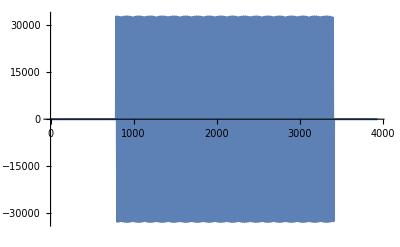

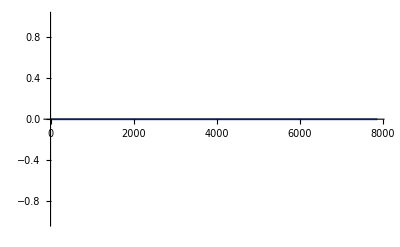

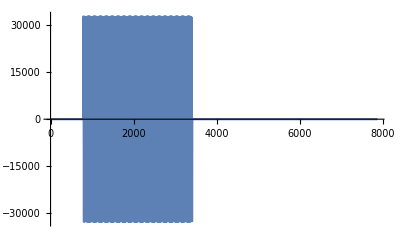

```mathematica
ListLinePlot[data[[1,;;Round[comSampling*15/1000]]]]
ListLinePlot[data[[2,;;Round[sampling*15/1000]]]]
ListLinePlot[data[[3,;;Round[sampling*15/1000]]]]
```

```mathematica
Depth[data]
```

3